```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"./modelFiles/SMS-stop_FA/SMS-stop_FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
processGGtt =  { V[4],V[4]} -> {-F[9], F[9]};
tops = CreateTopologies[1, 2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
allDiags = InsertFields[tops,processGGtt, InsertionLevel-> {Particles},ExcludeParticles->{F[12],V[1],V[2],V[3]},LastSelections->{S[4]}];
```

in total: 13 Particles insertions

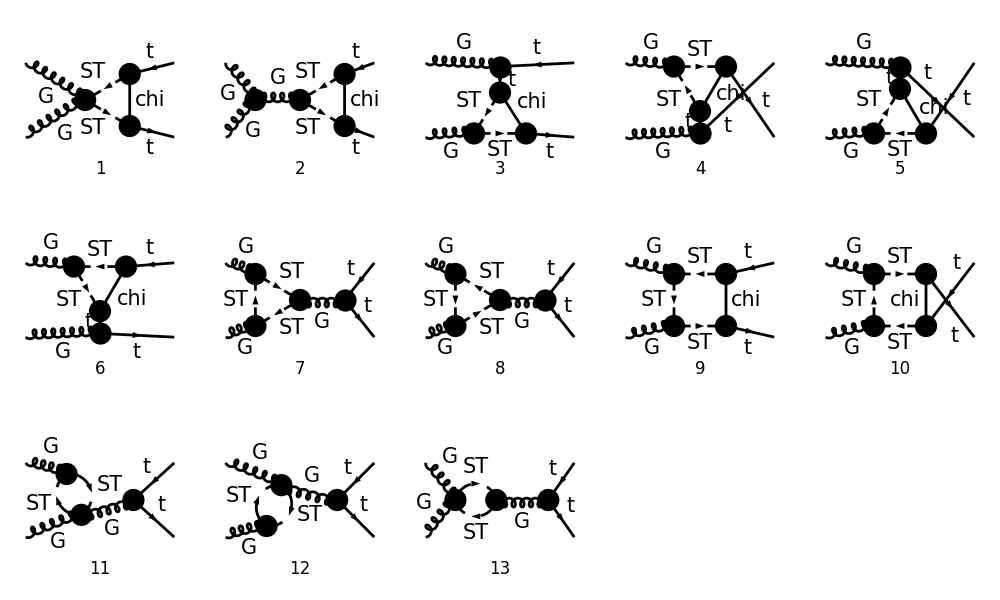

```mathematica
Paint[allDiags,ColumnsXRows->{5,3},ImageSize->{ 1000,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

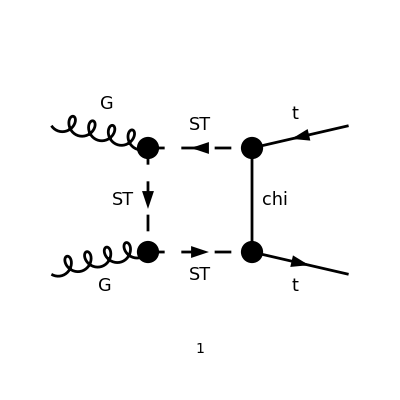

```mathematica
diags=DiagramExtract[allDiags,{9}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{400,200},Numbering->Simple];
```

```mathematica
(* Set Truncated->True to remove external fields  *)
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1,Truncated->True]//.{SUNT->FASUNT},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->False,TransversePolarizationVectors->{p1,p2},DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

(GS^2 (p2+2 q)^ν T_Col5Col3^Glu1 T_Col4Col5^Glu2 (k1+k2-p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(γ·(k2-p2-q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((p2+q)^2-mST^2).((-k2+p2+q)^2-mChi^2).((-k1-k2+p2+q)^2-mST^2))

```mathematica
PT =1/2( MTD[μ,ν]-FVD[p1,ν]FVD[p2,μ]/ScalarProduct[p1,p2]);
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,k1,k2,0,0,MT,MT];
(*ScalarProduct[k1,k2]=s/2-MT^2;
ScalarProduct[p1,p1]=0;
ScalarProduct[p2,p2]=0;
ScalarProduct[p1,p2]=s/2;
ScalarProduct[k1,k1]=MT^2;
ScalarProduct[k2,k2]=MT^2;
ScalarProduct[k1,p1]=(MT^2-t)/2;
ScalarProduct[k2,p1]=(MT^2-u)/2;
ScalarProduct[k2,p2]=(MT^2-t)/2;
ScalarProduct[k1,p2]=(MT^2-u)/2;*)
```

```mathematica
amp[1]=(Contract[PT SUNSimplify[FCTraceFactor[ amp[0]]]]/.{u-> 2 MT^2 -s-t})//Simplify
```

-(GS.GS yDM^2 (T^Glu2 T^Glu1)_Col4Col3 (γ̄)^7.(γ·(k2-p2-q)+mChi).(γ̄)^6 (s (k1·q)+s (k2·q)+4 (p1·q) (p2·q)+s (p1·q)-s (p2·q)-2 q^2 s))/(s (q^2-mST^2).((p2+q)^2-mST^2).((-k2+p2+q)^2-mChi^2).((-k1-k2+p2+q)^2-mST^2))

```mathematica
amp[2]=FullSimplify[DiracSimplify[amp[1]]]
```

-(GS.GS yDM^2 (T^Glu2 T^Glu1)_Col4Col3 ((γ·k2).(γ̄)^6-(γ·p2).(γ̄)^6-(γ·q).(γ̄)^6) (s (k1·q)+s (k2·q)+4 (p1·q) (p2·q)+s (p1·q)-s (p2·q)-2 q^2 s))/(s (q^2-mST^2).((p2+q)^2-mST^2).((k2-p2-q)^2-mChi^2).((k1+k2-p2-q)^2-mST^2))

```mathematica
amp[3]=TID[amp[2],q,ToPaVe->True]//Simplify
```

14+B_0(2 MT^2+s-t-u,mST^2,mST^2) (-1/1+110+1/1)+B_0(2 MT^2-t,mChi^2,mST^2) (-(ⅈ (D-1) π^2 (-(-(3 MT^2)/2-s/2+t+u/2) mChi^2+3 (2 MT^2-t) (2 MT^2+s-t-u)+mST^2 (-(3 MT^2)/2-s/2+t+u/2)+2 MT^2 (-(3 MT^2)/2-s/2+t+u/2)-t (-(3 MT^2)/2-s/2+t+u/2)) (MT^2+s/2-t/2-u/2) yDM^2 GS.GS (γ·(-k1-k2+p2)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 MT^4)/(2 (2-D) s (2 MT^2-t) ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u))^2)-(ⅈ π^2 (-(-(3 MT^2)/2-s/2+t+u/2) mChi^2+3 (2 MT^2-t) (2 MT^2+s-t-u)+mST^2 (-(3 MT^2)/2-s/2+t+u/2)+2 MT^2 (-(3 MT^2)/2-s/2+t+u/2)-t (-(3 MT^2)/2-s/2+t+u/2)) yDM^2 GS.GS γ^($AL($36806)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 MT^3)/(2 (2-D) s (2 MT^2-t) ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u)))+(ⅈ (D-1) π^2 (-(-(3 MT^2)/2-s/2+t+u/2) mChi^2+3 (2 MT^2-t) (2 MT^2+s-t-u)+mST^2 (-(3 MT^2)/2-s/2+t+u/2)+2 MT^2 (-(3 MT^2)/2-s/2+t+u/2)-t (-(3 MT^2)/2-s/2+t+u/2)) (MT^2+s/2-t/2-u/2) (-MT^2/2-s/2+u/2) yDM^2 GS.GS (γ·k1).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 MT^2)/(2 (2-D) s (2 MT^2-t) ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u))^2)+(ⅈ π^2 yDM^2 GS.GS (γ·p2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 MT^2)/(4 (t/2-MT^2/2)^2)+(ⅈ π^2 (2 MT^2+s-t-u) yDM^2 GS.GS (γ·(-k1-k2+p2)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 MT^2)/(2 s ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u)))+(2 ⅈ π^2 (MT^2 (2 MT^2+s-t-u)-(-MT^2/2-s/2+u/2)^2) (MT^2+s/2-t/2-u/2) yDM^2 GS.GS (γ·(-k1-k2+p2)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 MT^2)/((2-D) s ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u))^2)+110+(ⅈ π^2 (2 MT^2+s-t-u) (-MT^2/2-s/2+u/2) yDM^2 GS.GS (γ·(-k1-k2+p2)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(2 s ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u)))+(2 ⅈ π^2 (t/2-MT^2/2) (-MT^2/2-s/2+u/2) yDM^2 GS.GS (γ·(-k1-k2+p2)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/((2-D) s ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u)))-(ⅈ π^2 (-(2 MT^2+s-t-u) MT^2-D (-MT^2/2-s/2+u/2)^2+2 (-MT^2/2-s/2+u/2)^2) (MT^2+s/2-t/2-u/2) ((MT^2/2-s/2+u/2) mChi^2-mST^2 (MT^2/2-s/2+u/2)-2 MT^2 (MT^2/2-s/2+u/2)+t (MT^2/2-s/2+u/2)+(2 MT^2-t) (mChi^2-mST^2-2 MT^2-s+u)) yDM^2 GS.GS (γ·(-k1-k2+p2)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(2 (2-D) s (2 MT^2-t) ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u))^2)-(ⅈ (D-1) π^2 (t/2-MT^2/2) (2 MT^2+s-t-u) (-MT^2/2-s/2+u/2) ((MT^2/2-s/2+u/2) mChi^2-mST^2 (MT^2/2-s/2+u/2)-2 MT^2 (MT^2/2-s/2+u/2)+t (MT^2/2-s/2+u/2)+(2 MT^2-t) (mChi^2-mST^2-2 MT^2-s+u)) yDM^2 GS.GS (γ·(-k1-k2+p2)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(2 (2-D) s (2 MT^2-t) ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u))^2)+(ⅈ π^2 (t/2-MT^2/2) (-D (2 MT^2+s-t-u) MT^2+2 (2 MT^2+s-t-u) MT^2-D (-MT^2/2-s/2+u/2)^2) ((-(3 MT^2)/2-s/2+t+u/2) mChi^2-mST^2 (-(3 MT^2)/2-s/2+t+u/2)-2 MT^2 (-(3 MT^2)/2-s/2+t+u/2)+t (-(3 MT^2)/2-s/2+t+u/2)+(2 MT^2-t) (mChi^2-mST^2-5 MT^2-2 s+2 t+2 u)) yDM^2 GS.GS (γ·(-k1-k2+p2)).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(2 (2-D) s (2 MT^2-t) ((-MT^2/2-s/2+u/2)^2-MT^2 (2 MT^2+s-t-u))^2))
 |  |  |  |

```mathematica
(* Make sure there are no divergences *)
UVpart = PaXEvaluateUV[amp[3]]
```

((ⅈ π^2 (MT^2-t) (-4 MT^4-3 s MT^2+2 t MT^2+2 u MT^2+s^2-s u) yDM^2 GS.GS (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 (2 MT^2-t-u)^5)/(4 s (-7 MT^4-2 s MT^2+4 t MT^2+2 u MT^2+s^2+u^2-2 s u) (-4 MT^6+s MT^4+4 t MT^4+4 u MT^4-t^2 MT^2-u^2 MT^2-s t MT^2-s u MT^2-2 t u MT^2+s t u)^2)-(ⅈ π^2 (MT^2-u) (1) yDM^2 GS.GS (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 (2 MT^2-t-u)^5)/(4 s (-7 MT^4-2 s MT^2+4 t MT^2+2 u MT^2+s^2+u^2-2 s u) (-4 MT^6+13+s t u)^2)+401+(ⅈ π^2 3 (T^Glu2 T^Glu1)_Col4Col3)/(128 ((MT^2-s/2)^2-MT^4)^2 (4 MT^2-s) s^2 (s (1)^2+s (1) (1)+MT^2 1^2)^2 (2 MT^2-t-u)))/ε_UV
 |  |  |  |

```mathematica
Simplify[UVpart,Assumptions->{s>0,t>0,u>0,MT>0,mST>0,mChi>0}]
```

-((ⅈ π^2 yDM^2 GS.GS (112 (γ·(-k1-k2)).(γ̄)^6 MT^14+112 (γ·(k1+k2)).(γ̄)^6 MT^14+4 s (γ·(-k1-k2)).(γ̄)^6 MT^12-400 t (γ·(-k1-k2)).(γ̄)^6 MT^12-88 u (γ·(-k1-k2)).(γ̄)^6 MT^12+4 s (γ·(k1+k2)).(γ̄)^6 MT^12-400 t (γ·(k1+k2)).(γ̄)^6 MT^12-88 u (γ·(k1+k2)).(γ̄)^6 MT^12-80 mChi^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^12+80 mST^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^12-80 mChi^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^12+80 mST^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^12-80 s^2 (γ·(-k1-k2)).(γ̄)^6 MT^10+528 t^2 (γ·(-k1-k2)).(γ̄)^6 MT^10-28 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^10+4 s t (γ·(-k1-k2)).(γ̄)^6 MT^10+38 s u (γ·(-k1-k2)).(γ̄)^6 MT^10+324 t u (γ·(-k1-k2)).(γ̄)^6 MT^10-80 s^2 (γ·(k1+k2)).(γ̄)^6 MT^10+528 t^2 (γ·(k1+k2)).(γ̄)^6 MT^10-28 u^2 (γ·(k1+k2)).(γ̄)^6 MT^10+4 s t (γ·(k1+k2)).(γ̄)^6 MT^10+38 s u (γ·(k1+k2)).(γ̄)^6 MT^10+324 t u (γ·(k1+k2)).(γ̄)^6 MT^10+40 mChi^2 s (γ·(k1+k2-p2)).(γ̄)^6 MT^10-40 mST^2 s (γ·(k1+k2-p2)).(γ̄)^6 MT^10+176 mChi^2 t (γ·(k1+k2-p2)).(γ̄)^6 MT^10-176 mST^2 t (γ·(k1+k2-p2)).(γ̄)^6 MT^10+80 mChi^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^10-80 mST^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^10+40 mChi^2 s (γ·(-k1-k2+p2)).(γ̄)^6 MT^10-40 mST^2 s (γ·(-k1-k2+p2)).(γ̄)^6 MT^10+176 mChi^2 t (γ·(-k1-k2+p2)).(γ̄)^6 MT^10-176 mST^2 t (γ·(-k1-k2+p2)).(γ̄)^6 MT^10+80 mChi^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^10-80 mST^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^10+2 s^3 (γ·(-k1-k2)).(γ̄)^6 MT^8-332 t^3 (γ·(-k1-k2)).(γ̄)^6 MT^8+30 u^3 (γ·(-k1-k2)).(γ̄)^6 MT^8-43 s t^2 (γ·(-k1-k2)).(γ̄)^6 MT^8-24 s u^2 (γ·(-k1-k2)).(γ̄)^6 MT^8+8 t u^2 (γ·(-k1-k2)).(γ̄)^6 MT^8+188 s^2 t (γ·(-k1-k2)).(γ̄)^6 MT^8+20 s^2 u (γ·(-k1-k2)).(γ̄)^6 MT^8-362 t^2 u (γ·(-k1-k2)).(γ̄)^6 MT^8-107 s t u (γ·(-k1-k2)).(γ̄)^6 MT^8+2 s^3 (γ·(k1+k2)).(γ̄)^6 MT^8-332 t^3 (γ·(k1+k2)).(γ̄)^6 MT^8+30 u^3 (γ·(k1+k2)).(γ̄)^6 MT^8-43 s t^2 (γ·(k1+k2)).(γ̄)^6 MT^8-24 s u^2 (γ·(k1+k2)).(γ̄)^6 MT^8+8 t u^2 (γ·(k1+k2)).(γ̄)^6 MT^8+188 s^2 t (γ·(k1+k2)).(γ̄)^6 MT^8+20 s^2 u (γ·(k1+k2)).(γ̄)^6 MT^8-362 t^2 u (γ·(k1+k2)).(γ̄)^6 MT^8-107 s t u (γ·(k1+k2)).(γ̄)^6 MT^8+11 mChi^2 s^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^8-11 mST^2 s^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^8-148 mChi^2 t^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^8+148 mST^2 t^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^8-4 mChi^2 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^8+4 mST^2 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^8-88 mChi^2 s t (γ·(k1+k2-p2)).(γ̄)^6 MT^8+88 mST^2 s t (γ·(k1+k2-p2)).(γ̄)^6 MT^8-72 mChi^2 s u (γ·(k1+k2-p2)).(γ̄)^6 MT^8+72 mST^2 s u (γ·(k1+k2-p2)).(γ̄)^6 MT^8-136 mChi^2 t u (γ·(k1+k2-p2)).(γ̄)^6 MT^8+136 mST^2 t u (γ·(k1+k2-p2)).(γ̄)^6 MT^8+11 mChi^2 s^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^8-11 mST^2 s^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^8-148 mChi^2 t^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^8+148 mST^2 t^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^8-4 mChi^2 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^8+4 mST^2 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^8-88 mChi^2 s t (γ·(-k1-k2+p2)).(γ̄)^6 MT^8+88 mST^2 s t (γ·(-k1-k2+p2)).(γ̄)^6 MT^8-72 mChi^2 s u (γ·(-k1-k2+p2)).(γ̄)^6 MT^8+72 mST^2 s u (γ·(-k1-k2+p2)).(γ̄)^6 MT^8-136 mChi^2 t u (γ·(-k1-k2+p2)).(γ̄)^6 MT^8+136 mST^2 t u (γ·(-k1-k2+p2)).(γ̄)^6 MT^8+12 s^4 (γ·(-k1-k2)).(γ̄)^6 MT^6+101 t^4 (γ·(-k1-k2)).(γ̄)^6 MT^6+54 s t^3 (γ·(-k1-k2)).(γ̄)^6 MT^6-6 s u^3 (γ·(-k1-k2)).(γ̄)^6 MT^6-43 t u^3 (γ·(-k1-k2)).(γ̄)^6 MT^6-150 s^2 t^2 (γ·(-k1-k2)).(γ̄)^6 MT^6+16 s^2 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^6+3 t^2 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^6+54 s t u^2 (γ·(-k1-k2)).(γ̄)^6 MT^6-17 s^3 t (γ·(-k1-k2)).(γ̄)^6 MT^6-22 s^3 u (γ·(-k1-k2)).(γ̄)^6 MT^6+163 t^3 u (γ·(-k1-k2)).(γ̄)^6 MT^6+126 s t^2 u (γ·(-k1-k2)).(γ̄)^6 MT^6-38 s^2 t u (γ·(-k1-k2)).(γ̄)^6 MT^6+12 s^4 (γ·(k1+k2)).(γ̄)^6 MT^6+101 t^4 (γ·(k1+k2)).(γ̄)^6 MT^6+54 s t^3 (γ·(k1+k2)).(γ̄)^6 MT^6-6 s u^3 (γ·(k1+k2)).(γ̄)^6 MT^6-43 t u^3 (γ·(k1+k2)).(γ̄)^6 MT^6-150 s^2 t^2 (γ·(k1+k2)).(γ̄)^6 MT^6+16 s^2 u^2 (γ·(k1+k2)).(γ̄)^6 MT^6+3 t^2 u^2 (γ·(k1+k2)).(γ̄)^6 MT^6+54 s t u^2 (γ·(k1+k2)).(γ̄)^6 MT^6-17 s^3 t (γ·(k1+k2)).(γ̄)^6 MT^6-22 s^3 u (γ·(k1+k2)).(γ̄)^6 MT^6+163 t^3 u (γ·(k1+k2)).(γ̄)^6 MT^6+126 s t^2 u (γ·(k1+k2)).(γ̄)^6 MT^6-38 s^2 t u (γ·(k1+k2)).(γ̄)^6 MT^6-8 mChi^2 s^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^6+8 mST^2 s^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^6+56 mChi^2 t^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^6-56 mST^2 t^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^6-16 mChi^2 u^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^6+16 mST^2 u^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^6+69 mChi^2 s t^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^6-69 mST^2 s t^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^6+29 mChi^2 s u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^6-29 mST^2 s u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^6+8 mChi^2 t u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^6-8 mST^2 t u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^6-5 mChi^2 s^2 t (γ·(k1+k2-p2)).(γ̄)^6 MT^6+5 mST^2 s^2 t (γ·(k1+k2-p2)).(γ̄)^6 MT^6+5 mChi^2 s^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^6-5 mST^2 s^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^6+80 mChi^2 t^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^6-80 mST^2 t^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^6+110 mChi^2 s t u (γ·(k1+k2-p2)).(γ̄)^6 MT^6-110 mST^2 s t u (γ·(k1+k2-p2)).(γ̄)^6 MT^6-8 mChi^2 s^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+8 mST^2 s^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+56 mChi^2 t^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-56 mST^2 t^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-16 mChi^2 u^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+16 mST^2 u^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+69 mChi^2 s t^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-69 mST^2 s t^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+29 mChi^2 s u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-29 mST^2 s u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+8 mChi^2 t u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-8 mST^2 t u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-5 mChi^2 s^2 t (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+5 mST^2 s^2 t (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+5 mChi^2 s^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-5 mST^2 s^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+80 mChi^2 t^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-80 mST^2 t^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^6+110 mChi^2 s t u (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-110 mST^2 s t u (γ·(-k1-k2+p2)).(γ̄)^6 MT^6-2 s^5 (γ·(-k1-k2)).(γ̄)^6 MT^4-12 t^5 (γ·(-k1-k2)).(γ̄)^6 MT^4-2 u^5 (γ·(-k1-k2)).(γ̄)^6 MT^4-25 s t^4 (γ·(-k1-k2)).(γ̄)^6 MT^4+4 s u^4 (γ·(-k1-k2)).(γ̄)^6 MT^4+2 t u^4 (γ·(-k1-k2)).(γ̄)^6 MT^4+48 s^2 t^3 (γ·(-k1-k2)).(γ̄)^6 MT^4-2 s^2 u^3 (γ·(-k1-k2)).(γ̄)^6 MT^4+24 t^2 u^3 (γ·(-k1-k2)).(γ̄)^6 MT^4+3 s t u^3 (γ·(-k1-k2)).(γ̄)^6 MT^4+24 s^3 t^2 (γ·(-k1-k2)).(γ̄)^6 MT^4-2 s^3 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^4+6 t^3 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^4-37 s t^2 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^4-22 s^2 t u^2 (γ·(-k1-k2)).(γ̄)^6 MT^4-18 s^4 t (γ·(-k1-k2)).(γ̄)^6 MT^4+4 s^4 u (γ·(-k1-k2)).(γ̄)^6 MT^4-26 t^4 u (γ·(-k1-k2)).(γ̄)^6 MT^4-65 s t^3 u (γ·(-k1-k2)).(γ̄)^6 MT^4+12 s^2 t^2 u (γ·(-k1-k2)).(γ̄)^6 MT^4+35 s^3 t u (γ·(-k1-k2)).(γ̄)^6 MT^4-2 s^5 (γ·(k1+k2)).(γ̄)^6 MT^4-12 t^5 (γ·(k1+k2)).(γ̄)^6 MT^4-2 u^5 (γ·(k1+k2)).(γ̄)^6 MT^4-25 s t^4 (γ·(k1+k2)).(γ̄)^6 MT^4+4 s u^4 (γ·(k1+k2)).(γ̄)^6 MT^4+2 t u^4 (γ·(k1+k2)).(γ̄)^6 MT^4+48 s^2 t^3 (γ·(k1+k2)).(γ̄)^6 MT^4-2 s^2 u^3 (γ·(k1+k2)).(γ̄)^6 MT^4+24 t^2 u^3 (γ·(k1+k2)).(γ̄)^6 MT^4+3 s t u^3 (γ·(k1+k2)).(γ̄)^6 MT^4+24 s^3 t^2 (γ·(k1+k2)).(γ̄)^6 MT^4-2 s^3 u^2 (γ·(k1+k2)).(γ̄)^6 MT^4+6 t^3 u^2 (γ·(k1+k2)).(γ̄)^6 MT^4-37 s t^2 u^2 (γ·(k1+k2)).(γ̄)^6 MT^4-22 s^2 t u^2 (γ·(k1+k2)).(γ̄)^6 MT^4-18 s^4 t (γ·(k1+k2)).(γ̄)^6 MT^4+4 s^4 u (γ·(k1+k2)).(γ̄)^6 MT^4-26 t^4 u (γ·(k1+k2)).(γ̄)^6 MT^4-65 s t^3 u (γ·(k1+k2)).(γ̄)^6 MT^4+12 s^2 t^2 u (γ·(k1+k2)).(γ̄)^6 MT^4+35 s^3 t u (γ·(k1+k2)).(γ̄)^6 MT^4+mChi^2 s^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-mST^2 s^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-8 mChi^2 t^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+8 mST^2 t^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+4 mChi^2 u^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-4 mST^2 u^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-22 mChi^2 s t^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+22 mST^2 s t^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+8 mChi^2 t u^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-8 mST^2 t u^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-4 mChi^2 s^2 t^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+4 mST^2 s^2 t^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-11 mChi^2 s^2 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+11 mST^2 s^2 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-4 mChi^2 t^2 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+4 mST^2 t^2 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^4-14 mChi^2 s t u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+14 mST^2 s t u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^4+8 mChi^2 s^3 t (γ·(k1+k2-p2)).(γ̄)^6 MT^4-8 mST^2 s^3 t (γ·(k1+k2-p2)).(γ̄)^6 MT^4+6 mChi^2 s^3 u (γ·(k1+k2-p2)).(γ̄)^6 MT^4-6 mST^2 s^3 u (γ·(k1+k2-p2)).(γ̄)^6 MT^4-16 mChi^2 t^3 u (γ·(k1+k2-p2)).(γ̄)^6 MT^4+16 mST^2 t^3 u (γ·(k1+k2-p2)).(γ̄)^6 MT^4-60 mChi^2 s t^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^4+60 mST^2 s t^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^4-19 mChi^2 s^2 t u (γ·(k1+k2-p2)).(γ̄)^6 MT^4+19 mST^2 s^2 t u (γ·(k1+k2-p2)).(γ̄)^6 MT^4+mChi^2 s^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-mST^2 s^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-8 mChi^2 t^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+8 mST^2 t^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+4 mChi^2 u^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-4 mST^2 u^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-22 mChi^2 s t^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+22 mST^2 s t^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+8 mChi^2 t u^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-8 mST^2 t u^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-4 mChi^2 s^2 t^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+4 mST^2 s^2 t^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-11 mChi^2 s^2 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+11 mST^2 s^2 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-4 mChi^2 t^2 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+4 mST^2 t^2 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-14 mChi^2 s t u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+14 mST^2 s t u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+8 mChi^2 s^3 t (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-8 mST^2 s^3 t (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+6 mChi^2 s^3 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-6 mST^2 s^3 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-16 mChi^2 t^3 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+16 mST^2 t^3 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-60 mChi^2 s t^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+60 mST^2 s t^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^4-19 mChi^2 s^2 t u (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+19 mST^2 s^2 t u (γ·(-k1-k2+p2)).(γ̄)^6 MT^4+4 s t^5 (γ·(-k1-k2)).(γ̄)^6 MT^2+t u^5 (γ·(-k1-k2)).(γ̄)^6 MT^2-5 s^2 t^4 (γ·(-k1-k2)).(γ̄)^6 MT^2-t^2 u^4 (γ·(-k1-k2)).(γ̄)^6 MT^2-2 s t u^4 (γ·(-k1-k2)).(γ̄)^6 MT^2-10 s^3 t^3 (γ·(-k1-k2)).(γ̄)^6 MT^2-5 t^3 u^3 (γ·(-k1-k2)).(γ̄)^6 MT^2-2 s t^2 u^3 (γ·(-k1-k2)).(γ̄)^6 MT^2+s^2 t u^3 (γ·(-k1-k2)).(γ̄)^6 MT^2+6 s^4 t^2 (γ·(-k1-k2)).(γ̄)^6 MT^2-3 t^4 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^2+6 s t^3 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^2+11 s^2 t^2 u^2 (γ·(-k1-k2)).(γ̄)^6 MT^2+3 s^3 t u^2 (γ·(-k1-k2)).(γ̄)^6 MT^2+3 s^5 t (γ·(-k1-k2)).(γ̄)^6 MT^2+12 s t^4 u (γ·(-k1-k2)).(γ̄)^6 MT^2+5 s^2 t^3 u (γ·(-k1-k2)).(γ̄)^6 MT^2-14 s^3 t^2 u (γ·(-k1-k2)).(γ̄)^6 MT^2-6 s^4 t u (γ·(-k1-k2)).(γ̄)^6 MT^2+4 s t^5 (γ·(k1+k2)).(γ̄)^6 MT^2+t u^5 (γ·(k1+k2)).(γ̄)^6 MT^2-5 s^2 t^4 (γ·(k1+k2)).(γ̄)^6 MT^2-t^2 u^4 (γ·(k1+k2)).(γ̄)^6 MT^2-2 s t u^4 (γ·(k1+k2)).(γ̄)^6 MT^2-10 s^3 t^3 (γ·(k1+k2)).(γ̄)^6 MT^2-5 t^3 u^3 (γ·(k1+k2)).(γ̄)^6 MT^2-2 s t^2 u^3 (γ·(k1+k2)).(γ̄)^6 MT^2+s^2 t u^3 (γ·(k1+k2)).(γ̄)^6 MT^2+6 s^4 t^2 (γ·(k1+k2)).(γ̄)^6 MT^2-3 t^4 u^2 (γ·(k1+k2)).(γ̄)^6 MT^2+6 s t^3 u^2 (γ·(k1+k2)).(γ̄)^6 MT^2+11 s^2 t^2 u^2 (γ·(k1+k2)).(γ̄)^6 MT^2+3 s^3 t u^2 (γ·(k1+k2)).(γ̄)^6 MT^2+3 s^5 t (γ·(k1+k2)).(γ̄)^6 MT^2+12 s t^4 u (γ·(k1+k2)).(γ̄)^6 MT^2+5 s^2 t^3 u (γ·(k1+k2)).(γ̄)^6 MT^2-14 s^3 t^2 u (γ·(k1+k2)).(γ̄)^6 MT^2-6 s^4 t u (γ·(k1+k2)).(γ̄)^6 MT^2+2 mChi^2 s t^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-2 mST^2 s t^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-mChi^2 s u^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^2+mST^2 s u^4 (γ·(k1+k2-p2)).(γ̄)^6 MT^2+2 mChi^2 s^2 t^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-2 mST^2 s^2 t^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^2+mChi^2 s^2 u^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-mST^2 s^2 u^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-6 mChi^2 s t u^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^2+6 mST^2 s t u^3 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-mChi^2 s^3 t^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^2+mST^2 s^3 t^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^2+mChi^2 s^3 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-mST^2 s^3 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^2+mChi^2 s t^2 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-mST^2 s t^2 u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^2+11 mChi^2 s^2 t u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-11 mST^2 s^2 t u^2 (γ·(k1+k2-p2)).(γ̄)^6 MT^2-mChi^2 s^4 t (γ·(k1+k2-p2)).(γ̄)^6 MT^2+mST^2 s^4 t (γ·(k1+k2-p2)).(γ̄)^6 MT^2-mChi^2 s^4 u (γ·(k1+k2-p2)).(γ̄)^6 MT^2+mST^2 s^4 u (γ·(k1+k2-p2)).(γ̄)^6 MT^2+12 mChi^2 s t^3 u (γ·(k1+k2-p2)).(γ̄)^6 MT^2-12 mST^2 s t^3 u (γ·(k1+k2-p2)).(γ̄)^6 MT^2+10 mChi^2 s^2 t^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^2-10 mST^2 s^2 t^2 u (γ·(k1+k2-p2)).(γ̄)^6 MT^2-4 mChi^2 s^3 t u (γ·(k1+k2-p2)).(γ̄)^6 MT^2+4 mST^2 s^3 t u (γ·(k1+k2-p2)).(γ̄)^6 MT^2+2 mChi^2 s t^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-2 mST^2 s t^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-mChi^2 s u^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+mST^2 s u^4 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+2 mChi^2 s^2 t^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-2 mST^2 s^2 t^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+mChi^2 s^2 u^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-mST^2 s^2 u^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-6 mChi^2 s t u^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+6 mST^2 s t u^3 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-mChi^2 s^3 t^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+mST^2 s^3 t^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+mChi^2 s^3 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-mST^2 s^3 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+mChi^2 s t^2 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-mST^2 s t^2 u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+11 mChi^2 s^2 t u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-11 mST^2 s^2 t u^2 (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-mChi^2 s^4 t (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+mST^2 s^4 t (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-mChi^2 s^4 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+mST^2 s^4 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+12 mChi^2 s t^3 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-12 mST^2 s t^3 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+10 mChi^2 s^2 t^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-10 mST^2 s^2 t^2 u (γ·(-k1-k2+p2)).(γ̄)^6 MT^2-4 mChi^2 s^3 t u (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+4 mST^2 s^3 t u (γ·(-k1-k2+p2)).(γ̄)^6 MT^2+(4 MT^2-s) (2 MT^2-t) (28 MT^10+(s-44 t-36 u) MT^8+(-6 s^2+3 (t+3 u) s+23 t^2+11 u^2+38 t u) MT^6+(s^3+(6 t+4 u) s^2-(2 t^2+17 u t+7 u^2) s+2 (-2 t^3-5 u t^2-2 u^2 t+u^3)) MT^4-((t+u) s^3+(t^2+2 u t-u^2) s^2-u (6 t^2+5 u t+u^2) s+u^2 (t+u)^2) MT^2+s t (s-u)^2 u) γ^($AL($36805)).(γ̄)^6 MT-(4 MT^2-s) (2 MT^2-t) (28 MT^10+(s-44 t-36 u) MT^8+(-6 s^2+3 (t+3 u) s+23 t^2+11 u^2+38 t u) MT^6+(s^3+(6 t+4 u) s^2-(2 t^2+17 u t+7 u^2) s+2 (-2 t^3-5 u t^2-2 u^2 t+u^3)) MT^4-((t+u) s^3+(t^2+2 u t-u^2) s^2-u (6 t^2+5 u t+u^2) s+u^2 (t+u)^2) MT^2+s t (s-u)^2 u) γ^($AL($36806)).(γ̄)^6 MT+s^3 t^4 (γ·(-k1-k2)).(γ̄)^6+s t^3 u^3 (γ·(-k1-k2)).(γ̄)^6-s^5 t^2 (γ·(-k1-k2)).(γ̄)^6+s t^4 u^2 (γ·(-k1-k2)).(γ̄)^6-2 s^2 t^3 u^2 (γ·(-k1-k2)).(γ̄)^6-s^3 t^2 u^2 (γ·(-k1-k2)).(γ̄)^6-2 s^2 t^4 u (γ·(-k1-k2)).(γ̄)^6+s^3 t^3 u (γ·(-k1-k2)).(γ̄)^6+2 s^4 t^2 u (γ·(-k1-k2)).(γ̄)^6+s^3 t^4 (γ·(k1+k2)).(γ̄)^6+s t^3 u^3 (γ·(k1+k2)).(γ̄)^6-s^5 t^2 (γ·(k1+k2)).(γ̄)^6+s t^4 u^2 (γ·(k1+k2)).(γ̄)^6-2 s^2 t^3 u^2 (γ·(k1+k2)).(γ̄)^6-s^3 t^2 u^2 (γ·(k1+k2)).(γ̄)^6-2 s^2 t^4 u (γ·(k1+k2)).(γ̄)^6+s^3 t^3 u (γ·(k1+k2)).(γ̄)^6+2 s^4 t^2 u (γ·(k1+k2)).(γ̄)^6+mChi^2 s^2 t u^3 (γ·(k1+k2-p2)).(γ̄)^6-mST^2 s^2 t u^3 (γ·(k1+k2-p2)).(γ̄)^6-2 mChi^2 s^3 t u^2 (γ·(k1+k2-p2)).(γ̄)^6+2 mST^2 s^3 t u^2 (γ·(k1+k2-p2)).(γ̄)^6-2 mChi^2 s^2 t^3 u (γ·(k1+k2-p2)).(γ̄)^6+2 mST^2 s^2 t^3 u (γ·(k1+k2-p2)).(γ̄)^6+mChi^2 s^4 t u (γ·(k1+k2-p2)).(γ̄)^6-mST^2 s^4 t u (γ·(k1+k2-p2)).(γ̄)^6+mChi^2 s^2 t u^3 (γ·(-k1-k2+p2)).(γ̄)^6-mST^2 s^2 t u^3 (γ·(-k1-k2+p2)).(γ̄)^6-2 mChi^2 s^3 t u^2 (γ·(-k1-k2+p2)).(γ̄)^6+2 mST^2 s^3 t u^2 (γ·(-k1-k2+p2)).(γ̄)^6-2 mChi^2 s^2 t^3 u (γ·(-k1-k2+p2)).(γ̄)^6+2 mST^2 s^2 t^3 u (γ·(-k1-k2+p2)).(γ̄)^6+mChi^2 s^4 t u (γ·(-k1-k2+p2)).(γ̄)^6-mST^2 s^4 t u (γ·(-k1-k2+p2)).(γ̄)^6) (T^Glu2 T^Glu1)_Col4Col3)/(2 ε_UV (4 MT^2-s) s (2 MT^2-t) (7 MT^4+2 (s-2 t-u) MT^2-(s-u)^2) (4 MT^6-(s+4 (t+u)) MT^4+(t+u) (s+t+u) MT^2-s t u)))

```mathematica
amp[4]=ChangeDimension[amp[3],4]/.{D->4}//Simplify
```

1/(2 s)yDM^2 GS.GS (ⅈ π^2 (-(γ̄·(OverBar[k1]+OverBar[k2]))).(γ̄)^6 D_33(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) (-2 MT^2+t+u)^2-(2 (2 MT^2+s-t-u) (γ̄·OverBar[k1]).(γ̄)^6)/(((q̄)^2-mST^2).((q̄-OverBar[k1])^2-mChi^2).((-OverBar[k1]-OverBar[k2]+OverBar[p2]+q̄)^2-mST^2))+(s (γ̄·OverBar[k2]).(γ̄)^6)/(((q̄)^2-mST^2).((q̄-OverBar[k2])^2-mChi^2).((q̄-OverBar[p2])^2-mST^2))+((4 mST^2-s) s (γ̄·OverBar[k2]).(γ̄)^6)/(((q̄)^2-mST^2).((q̄-OverBar[k2])^2-mChi^2).((q̄-OverBar[p2])^2-mST^2).((-OverBar[k1]-OverBar[k2]+q̄)^2-mST^2))-ⅈ π^2 (2 MT^2-s-2 u) ((γ̄·OverBar[k1]).(γ̄)^6-(γ̄·OverBar[k2]).(γ̄)^6) C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+ⅈ π^2 s (γ̄·OverBar[k2]).(γ̄)^6 C_1(MT^2,2 MT^2-t,0,mST^2,mChi^2,mST^2)-2 ⅈ π^2 (3 MT^2+s-2 t-u) (γ̄·OverBar[k1]).(γ̄)^6 C_1(MT^2,2 MT^2-t,2 MT^2+s-t-u,mST^2,mChi^2,mST^2)-ⅈ π^2 (2 MT^4-(t+3 u) MT^2+s^2+u^2-4 mST^2 s+t u) (γ̄·OverBar[k2]).(γ̄)^6 D_1(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)+ⅈ π^2 s (γ̄·OverBar[p2]).(γ̄)^6 C_2(MT^2,2 MT^2-t,0,mST^2,mChi^2,mST^2)-2 ⅈ π^2 (2 MT^2+s-t-u) ((γ̄·OverBar[k1]).(γ̄)^6-(-(γ̄·(OverBar[k1]+OverBar[k2]-OverBar[p2]))).(γ̄)^6) C_2(MT^2,2 MT^2-t,2 MT^2+s-t-u,mST^2,mChi^2,mST^2)-ⅈ π^2 s ((-2 MT^2+t+u) (γ̄·OverBar[k2]).(γ̄)^6+(s-4 mST^2) (γ̄·OverBar[p2]).(γ̄)^6) D_2(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)-ⅈ π^2 ((γ̄·OverBar[k2]).(γ̄)^6 (-2 MT^2+t+u)^2+(4 mST^2-s) s (-(γ̄·(OverBar[k1]+OverBar[k2]))).(γ̄)^6) D_3(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)-4 ⅈ π^2 (γ̄·OverBar[p1]).(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+4 ⅈ π^2 (γ̄·OverBar[p1]).(γ̄)^6 C_00(MT^2,2 MT^2-t,2 MT^2+s-t-u,mST^2,mChi^2,mST^2)+2 ⅈ π^2 (2 MT^2-t-u) (γ̄·OverBar[p1]).(γ̄)^6 D_00(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)+2 ⅈ π^2 ((MT^2-t) (γ̄·OverBar[k1]).(γ̄)^6+(MT^2-u) (γ̄·OverBar[k2]).(γ̄)^6) C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-2 ⅈ π^2 (MT^2-t) (γ̄·OverBar[k1]).(γ̄)^6 C_11(MT^2,2 MT^2-t,2 MT^2+s-t-u,mST^2,mChi^2,mST^2)-ⅈ π^2 (MT^2-u) (2 MT^2-t-u) (γ̄·OverBar[k2]).(γ̄)^6 D_11(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)-2 ⅈ π^2 ((MT^2-u) (γ̄·OverBar[k1]).(γ̄)^6+(MT^2-t) (γ̄·OverBar[k2]).(γ̄)^6) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-2 ⅈ π^2 ((2 MT^2+s-t-u) (γ̄·OverBar[k1]).(γ̄)^6+(t-MT^2) (-(γ̄·(OverBar[k1]+OverBar[k2]-OverBar[p2]))).(γ̄)^6) C_12(MT^2,2 MT^2-t,2 MT^2+s-t-u,mST^2,mChi^2,mST^2)+ⅈ π^2 (2 MT^2-t-u) (s (γ̄·OverBar[k2]).(γ̄)^6+(u-MT^2) (γ̄·OverBar[p2]).(γ̄)^6) D_12(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)-ⅈ π^2 (2 MT^2-t-u) ((2 MT^2-t-u) (γ̄·OverBar[k2]).(γ̄)^6+(u-MT^2) (-(γ̄·(OverBar[k1]+OverBar[k2]))).(γ̄)^6) D_13(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)+2 ⅈ π^2 (2 MT^2+s-t-u) (-(γ̄·(OverBar[k1]+OverBar[k2]-OverBar[p2]))).(γ̄)^6 C_22(MT^2,2 MT^2-t,2 MT^2+s-t-u,mST^2,mChi^2,mST^2)+ⅈ π^2 s (2 MT^2-t-u) (γ̄·OverBar[p2]).(γ̄)^6 D_22(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)-ⅈ π^2 (2 MT^2-t-u) (s (-(γ̄·(OverBar[k1]+OverBar[k2]))).(γ̄)^6+(2 MT^2-t-u) (γ̄·OverBar[p2]).(γ̄)^6) D_23(MT^2,2 MT^2-t,2 MT^2+s-t-u,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2)) (T^Glu2 T^Glu1)_Col4Col3

```mathematica
amp[5]=Simplify[PaXEvaluate[amp[3],PaXC0Expand->True,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],Assumptions-> {s>0,MT>0}]
```

-(ⅈ aS MT yt δ^Glu1Glu2 ((4 MT^2-s) log^2((√(s (s-4 MT^2))+2 MT^2-s)/(2 MT^2))+4 s))/(4 √2 π s)

#### Check Final Result:

```mathematica
resCheck=Simplify[amp[5]//.{s-> 4 MT^2/ρ,yt-> MT/Subscript[v, H],Subscript[v, H]-> 1/(√(√2 Subscript[G, F]))},Assumptions->{ρ>0,MT>0}]
```

-(ⅈ aS MT^2 √G_F ((ρ-1) log^2((ρ+2 √(1-ρ)-2)/ρ)+4) δ^Glu1Glu2)/(4 2^(1/4) π)

Correct answer (check Eq. 2.5 and 2.6  from S. Bock thesis) for ρ > 1:

```mathematica
answer1=(-I(SUNTrace[SUNT[Glu1,Glu2]]))/(4 Pi)√(√2 Subscript[G, F])aS MT (2 MT +MT (4 MT^2 - MH^2)(1/(2 MH^2))(Log[(1+√(1-ρ))/(1-√(1-ρ))]-I Pi)^2)/.{MH-> √(4 MT^2/ρ)}//
Simplify
```

-(ⅈ aS MT^2 √G_F (4+(ρ-1) (log((√(1-ρ)+1)/(1-√(1-ρ)))-ⅈ π)^2) δ^Glu1Glu2)/(8 2^(3/4) π)

```mathematica
(* Not sure where the 2 √2 factor comes from *)
FullSimplify[resCheck-2 √2 answer1,Assumptions->{ρ<1,ρ>0}]
```

0

#### EFT Limit (MT → ∞)

```mathematica
Series[resCheck/.ρ-> 4 MT^2/MH^2,{MT, Infinity,1}]
```

-(ⅈ aS MH^2 √G_F δ^Glu1Glu2)/(6 2^(1/4) π)+O((1/MT)^2)

#### Expansion using Package - X

```mathematica
Collect[Expand[PaXEvaluate[amp[3],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries-> {{s,0,2}}]],s,Simplify]
```

-(7 ⅈ aS s^2 yt δ^Glu1Glu2)/(720 √2 π MT^3)-(ⅈ aS s yt δ^Glu1Glu2)/(6 √2 π MT)